## Lesson 15: Mechanical Oscillations

## Overview

In the introduction to differential equations, you saw that differential equations can model a variety of physical phenomena.

Second-order linear equations are of particular importance because they can be used to describe mechanical vibrations and oscillations.

Newton’s second law states that the acceleration of a body, y''(t), is directly proportional to the force applied.

m y''(t)=∑F

What Newton was really describing was a second-order linear nonhomogeneous differential equation!

```mathematica
Manipulate[Grid[{{Show[ParametricPlot3D[{Sin[2*Pi*t],Cos[2*Pi*t],(t/10)*springHeight[a]},{t,0,10},],Graphics3D[Cuboid[{-1,-1,springHeight[a]-2},{1,1,springHeight[a]}]],],Show[Plot[springHeight[x],{x,0,10},],Graphics[]]}}],{a,1,10},Initialization:>(springHeight[t_]:=-Cos[t]-2)]
```

## Simple Harmonic Motion

The model described by Newton is well equipped to describe a variety of different harmonic oscillations.

This includes simple harmonic motion, damped oscillation and forced oscillations.

Consider a mass hanging from a spring, which at rest is elongated a length L.

```mathematica
springHeight[t_]:=-Cos[t]-2
Show[ParametricPlot3D[{Sin[2*Pi*t],Cos[2*Pi*t],(t/10)*springHeight[0]},{t,0,10},],Graphics3D[],Graphics3D[],Graphics3D[],]
```

-Graphics3D-

There are two forces acting on this object:

• The gravitational force 
	• The force of the spring

When the object is at rest, the acceleration is zero, so this can be represented by the equation:

0=m g+F_s

## Simple Harmonic Motion

When the mass is initially displaced, it is known from Newton’s second law that the following must always be true:

m y''(t)=m g+F_s

The force of the spring becomes larger as the spring is stretched out, so it can be said that it is proportional to the elongation.

This can be written as:

F_s=-k(L+y(t))

Now the equation becomes:

m y''(t)=m g-k(L+y(t))

Noting that m g-k L=0 and rearranging, the equation becomes a second-order homogeneous linear differential equation with constant coefficients:

m y''(t)+k y(t)=0

## Example: Simple Harmonic Motion

A mass that weighs 2 lbs stretches a spring 4 inches. Suppose the mass is displaced an additional 2 inches in the negative direction and then released. Solve for the differential equation that represents this physical setting and plot the solution.

The model under consideration is:

m y''(t)+k y(t)=0

First, solve for the spring constant, k:

F_s=-k(L+y(t))

Using the fact that at rest y(0)=0 and F_s=-mg:

-m g=-k(L+y(0))
	=-k L

Therefore,

```mathematica
m=Quantity[2,"Pounds"]/Quantity[, "StandardAccelerationOfGravity"]
```

2 lb/g

```mathematica
k=m*Quantity[, "StandardAccelerationOfGravity"]/Quantity[4,"Inches"]
```

1/2 lb/in

You can see in the statement of the problem that the spring is initially displaced 2 inches downward.

Thus, the initial value problem can be written as:

y''(t)+k/m y(t)=0

y(0)=-2 in

y'(0)=0 in/s

## Example: Simple Harmonic Motion

Now the solution can be found through DSolveValue.

First, calculate the quantity k/m:

```mathematica
km=UnitConvert[k/m,"Imperial"]//N
```

96.5221 per second^2

Substitute this into the equation, cancel the units and use DSolveValue:

```mathematica
sln=DSolveValue[{y''[t]+QuantityMagnitude[km] y[t]==0,y[0]==-2,y'[0]==0},y[t],t]
```

-2. Cos[9.82457 t]

Visualize the motion of the mass over time:

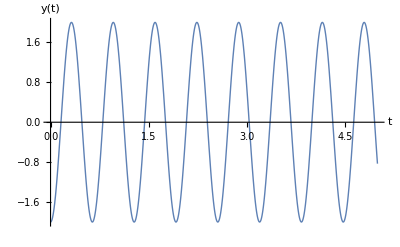

```mathematica
Plot[sln,{t,0,5},]
```

You can imagine how this represents the motion of an object oscillating on a spring.

## Example: Harmonic Motion with Damping

A mass that weighs 1 lb stretches a spring 6 inches. Suppose the mass is displaced an additional 2 inches in the negative direction and then released. The air resistance is proportional to the velocity with a proportionality constant 1/100(lb*s)/ft. Formulate the initial value problem associated with this description.

It is reasonable to assume that the resistance is always acting in the opposite direction of the object’s velocity:

F_d=-θ y'(t)

Now the model has transformed to become:

m y''(t)=-k y(t)-θ y'(t)

Calculate m and g in the same way as the previous example:

```mathematica
m=UnitConvert[Quantity[1,"Pounds"]/Quantity[, "StandardAccelerationOfGravity"],"Imperial"]
```

6096/196133 lb s^2/ft

```mathematica
k=UnitConvert[m*Quantity[, "StandardAccelerationOfGravity"]/Quantity[6,"Inches"],"Imperial"]
```

2 lb/ft

The proportionality constant θ is provided as:

```mathematica
θ=Quantity[1/100,("Pounds"*"Seconds")/"Feet"]
```

1/100 lb s/ft

Substituting these quantities into the equation:

```mathematica
m*y''[t]+θ*y'[t]+k*y[t]==0
```

(2 lb/ft) y[t]+(1/100 lb s/ft) y'[t]+(6096/196133 lb s^2/ft) y''[t]==0

Taking the magnitude of the quantities and canceling the units gives an equation describing the motion over time:

```mathematica
eqn=QuantityMagnitude[m]*y''[t]+QuantityMagnitude[θ]*y'[t]+QuantityMagnitude[k]*y[t]==0
```

2 y[t]+y'[t]/100+(6096 y''[t])/196133==0

## Example: Harmonic Motion with Damping

From the statement of the problem, you know that the spring is initially displaced 2 inches downward.

All that remains is to find the solution through DSolveValue:

```mathematica
sln=DSolveValue[{eqn,y[0]==-2/12,y'[0]==0},y[t],t]
```

-(ⅇ^(-196133 t/1219200) (487483867 Cos[(√95611673286311 t)/1219200]+√95611673286311 Sin[(√95611673286311 t)/1219200]))/2924903202

Plot the motion of the mass over time:

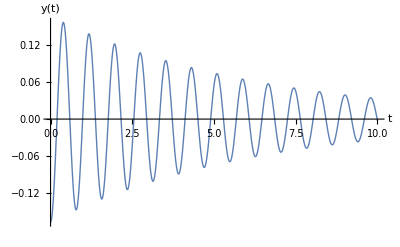

```mathematica
Plot[sln,{t,0,10},]
```

You can quite clearly observe the oscillations dampening gradually.

## Example: Harmonic Motion with External Forces

A mass that weighs 2 lbs stretches a spring 3 inches. Suppose the mass is displaced an additional 3 inches in the negative direction and then released. The air resistance is proportional to the velocity with a proportionality constant 1/50^(lb*s)/ft. There is an external force acting on the object with a force measured by the function 1/10 sin(x) lb*ft. Formulate the initial value problem associated with this description. Solve and plot the solution.

When there are additional external forces that are not described by the variations of the spring, the equation transforms to be a nonhomogeneous equation.

The equation is then rewritten as:

m y''(t)+θ y'(t)+k y(t)=F(t)

To make things easy, approximate g=32 ft/s^2 and use L=3 in=0.25 ft:

```mathematica
g=32;
L=0.25;
```

Use this value for g and L while canceling the units right away:

```mathematica
m=2/g
```

1/16

```mathematica
k=(m*g)/L
```

8.

Define the proportionality constant θ:

```mathematica
θ=1/50;
```

Substituting these quantities into the equation:

```mathematica
eqn=m*y''[t]+θ*y'[t]+k*y[t]==Sin[t]/10
```

8. y[t]+y'[t]/50+y''[t]/16==Sin[t]/10

## Example: Harmonic Motion with External Forces

From the statement of the problem, you know that the spring is initially displaced 3 inches downward.

All that remains is to find the solution through DSolveValue:

```mathematica
sln=DSolveValue[{eqn,y[0]==-3/12,y'[0]==0},y[t],t]
```

-0.000106368 ⅇ^(-0.16 t) (2350.04 Cos[11.3126 t]+1. ⅇ^(0.16 t) Cos[10.3126 t] Cos[11.3126 t]-0.701565 ⅇ^(0.16 t) Cos[11.3126 t] Cos[12.3126 t]+64.4536 ⅇ^(0.16 t) Cos[11.3126 t] Sin[10.3126 t]+43.7078 Sin[11.3126 t]-64.4536 ⅇ^(0.16 t) Cos[10.3126 t] Sin[11.3126 t]+53.9879 ⅇ^(0.16 t) Cos[12.3126 t] Sin[11.3126 t]+1. ⅇ^(0.16 t) Sin[10.3126 t] Sin[11.3126 t]-53.9879 ⅇ^(0.16 t) Cos[11.3126 t] Sin[12.3126 t]-0.701565 ⅇ^(0.16 t) Sin[11.3126 t] Sin[12.3126 t])

Visualize the solution:

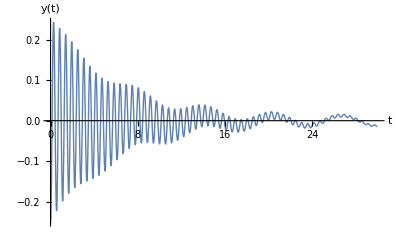

```mathematica
Plot[sln,{t,0,30},]
```

The height of the oscillations is clearly dampened gradually over time.

The external forcing terms are acting at a different period, and you can see that the period of the oscillations is gradually becoming dominated by the external forces.

## Electrical Circuits

What is rather fascinating is that this model for spring oscillations can also represent the flow of electric current in a LRC circuit.

The voltage drop across the resistor is:

V=I R

The voltage drop across the capacitor is:

V=Q/C

The voltage drop across the inductor is:

V=L I'(t)

Therefore, by Kirchhoff’s law:

L I'(t)+R I(t)+Q/C=E(t)

Since I(t)=Q'(t), the equation gets transformed into a second-order equation:

L Q''(t)+R Q'(t)+1/C Q(t)=E(t)

## Example: Electric Circuits

A series circuit has a capacitor of 0.25 *10^-6 F and an inductor of  1 H. The initial charge of the capacitor is 10^-6 C. If there is no initial current, find the charge Q on the capacitor at any time t.

Because there is no resistor or impressed current, the equation becomes:

L Q''(t)+1/C Q(t)=0

Take L=1 and C = 0.25*10^-6. The problem now appears to be much more simplified:

```mathematica
eqn=Q''[t]+1/(0.25 10^-6)Q[t]==0
```

4.×10^6 Q[t]+Q''[t]==0

It can be determined by the statement of the problem that there is no initial current.

The initial charge is given to be 10^-6 C.

Together these imply the initial conditions:

Q(0)=10^-6

Q'(0)=0

## Example: Electric Circuits

All that remains is to find the solution through DSolveValue:

```mathematica
sln=DSolveValue[{eqn,Q[0]==10^-6,Q'[0]==0},Q[t],t]
```

1.×10^-6 Cos[2000. t]

Visualize the flow of charge over time:

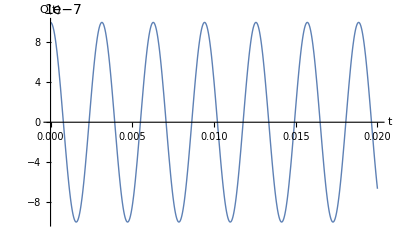

```mathematica
Plot[sln,{t,0,.02},]
```

Because there is no resistance in the circuit, you can see that the charge of the circuit oscillates evenly.

This is the type of behavior to be expected from this form of the model.

## Summary

Second-order differential equations can be used to model mechanical oscillations quite comprehensively.

Oscillations, air resistance and external forces can all be modeled as a single second-order linear nonhomogeneous differential equation taking the form:

m y''(t)+θ y'(t)+k y(t)=F(t)

Using the methods you have learned in the previous lessons, you can exactly solve these equations and draw conclusions about the behavior of a wide variety of physical systems.